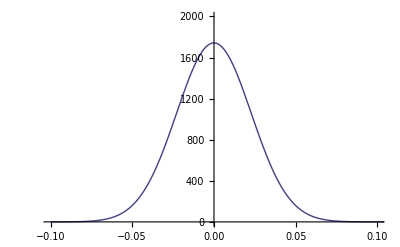

0.0580958

```mathematica
(*So this was used to calculate the bootstrapping confidence intervals. Bassically, after generating all the sample data sets using the bootstrap method and then fitting it with a gaussian, take thoes fit data and put them in here.  Integrate the normalized gaussian from the pearsons correlation coeeficient to inf to get one-tailed p-value. 2 times this for two tailed*)

a = 1.74249 10^3;
b =-5.19352 *10^-5;
c =2.28624 10^-2;
corr =0.04327173289933918;
Plot[a ⅇ^(-(x-b)^2/(2 c^2)),{x,-0.1,01},PlotRange->{{-.1,.1},{0,2000}}]
2*∫_corr^∞ 1/(c √(2 π)) ⅇ^(-(x-b)^2/(2 c^2))ⅆx
```